```mathematica
α=7.297352533 10^-3;
H[x_,y_,β_]:=(α*β)/(2*π)*(1/(√(x*(1-x)))*ArcTan[√(x/(1-x))]-1+π(λ[y,β] x)/(1-x-λ[y,β]^2)) Exp[-(2y)/β];
H0[x_,y_,β_]:= α*β*(1/(4 √(1-x))+1/2 λ[y,β]/(1-x-λ[y,β]^2)) Exp[-(2y)/β];
dH[x_,y_,β_]:=((x+(2 *x -1))/(2*x^2*(1-x)) √(x/(1-x))ArcTan[ √(x/(1-x))]+(π(1-λ[y,β])^2 λ[y,β])/((1-λ[y,β]^2-x)^2))Exp[-(2y)/β];
u1[y_,β_]:=(2 β^2)/(α^2 y^2)*Exp[ExpIntegralEi[-(2y)/β]];
λ[y_,β_]:= α/2 (Log[4.5 u1[y,β]]-2.44 Log[Log[0.15 u1[y,β]]]);
```

```mathematica
LDis2=Table[x/.FindRoot[x-y+H[x,y,100],{x,0.1,0.997},MaxIterations->1000],{y,0.0000000001,25,0.1}];
LDis21=Delete[LDis2,{{112},{158},{210},{211}}];
LDis3=Table[x/.FindRoot[x-y+H[x,y,100],{x,0.1,0.999},MaxIterations->1000],{y,25,100,0.1}];
LDis32=Delete[LDis3,{{243},{323},{324},{438},{439},{590},{591},{592},{593}}];
LDis5=Table[x/.FindRoot[x-y+H[x,y,100],{x,0.9999,0.99999999},MaxIterations->1000],{y,0.0000000001,100,0.1}];
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

General::stop: Further output of FindRoot::brmp will be suppressed during this calculation.

```mathematica
Pl21=ListInterpolation[Re[LDis21],{{0,25}}];
Pl22=ListInterpolation[Re[LDis32],{{25,100}}];
Pl24=ListInterpolation[Re[LDis5],{{0,100}}];
```

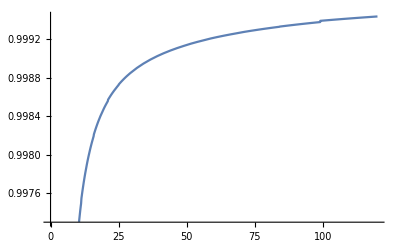

```mathematica
Fd[y_]:=Which[y<25,Pl21[y],25≤y≤99,Pl22[y],y>99,1-λ[y,100]^2];
Plot[Fd[y],{y,0,120}]
```

```mathematica
Fd2[y_]:=If[y<99,Pl24[y],1];
```

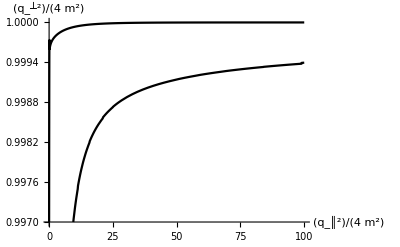

```mathematica
Plot[{Fd[y],Fd2[y]},{y,0,100},PlotRange->{0.997,1},PlotStyle->{Black},AxesLabel->{(q_║)^2/(4 m^2),(q_┴)^2/(4 m^2)}]
```

```mathematica
ξ[x_,y_,z_]:=(y-x+2*x1*√(z+x))/(2*x1*√y);M1[x_,y_,z_,β_]:=((2*π)/(α*β))^2*(√Abs[1-ξ[x,y,z]^2]*√(y*z)*(y-x-(α*β* λ[y,β] x)/(2(1-x-λ[y,β]^2))Exp[(-2y)/β])^2)/(x*√(x+z)((x1-√(x+z))^2-z))*UnitStep[1-ξ[x,y,z]]*UnitStep[y-x];
In1[x_,y_,z_,β_]:=M1[x,y,z,β]*(1+(α*β)/(2*π)*dH[x,y,β])^-1;
```

```mathematica
WW1={};x1=.;
For[x1=0, x1≤ 2.9,WW1=Append[WW1,{x1,NIntegrate[In1[Fd[y],y,z,100],{y,0,∞},{z,0,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 100000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.1];
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained -1.06667×10^-6 and 7.98142×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 9.18708×10^-6 and 0.0000102171 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
WW1
```

{{0.1,0.},{0.2,-1.06667×10^-6},{0.3,9.18708×10^-6},{0.4,0.0000178855},{0.5,0.0000532907},{0.6,0.000117656},{0.7,0.000398351},{0.8,0.00100309},{0.9,0.00297048},{1.,0.00906698},{1.1,0.023286},{1.2,0.0572078},{1.3,0.113766},{1.4,0.192151},{1.5,0.294149},{1.6,0.405138},{1.7,0.534995},{1.8,0.659426},{1.9,0.789344},{2.,0.935332},{2.1,1.0515},{2.2,1.17834},{2.3,1.29605},{2.4,1.40938},{2.5,1.52442},{2.6,1.61321},{2.7,1.68565},{2.8,1.75985},{2.9,1.81786},{3.,1.86235}}

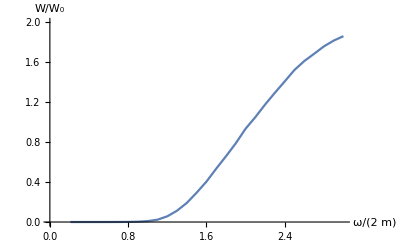

```mathematica
ListLinePlot[Re[WW1],PlotRange->{{0,3},{0,2}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

```mathematica
WW2={};x1=.;
For[x1=0, x1≤ 2.9,WW2=Append[WW2,{x1,NIntegrate[In1[Fd2[y],y,z,100],{y,0,∞},{z,0,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 100000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.1];
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
WW2
```

{{0.1,0.},{0.2,0.},{0.3,0.},{0.4,0.},{0.5,0.},{0.6,0.},{0.7,0.},{0.8,0.},{0.9,0.},{1.,0.},{1.1,0.00039572},{1.2,0.00266709},{1.3,0.00849395},{1.4,0.0189713},{1.5,0.0348423},{1.6,0.0564976},{1.7,0.0853672},{1.8,0.121669},{1.9,0.160535},{2.,0.210271},{2.1,0.262621},{2.2,0.326653},{2.3,0.389441},{2.4,0.455846},{2.5,0.52932},{2.6,0.602255},{2.7,0.67772},{2.8,0.758953},{2.9,0.836967},{3.,0.913983}}

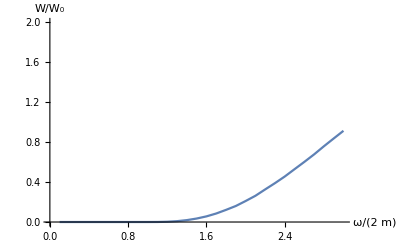

```mathematica
ListLinePlot[Re[WW2],PlotRange->{{0,3},{0,2}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

```mathematica
1->22
```

```mathematica
11
```

```mathematica
Dom0[x1_,kx_,ky_]:=(x1^2+Fd[kx^2+ky^2]-Fd[x1^2+kx^2+ky^2-2*x1*kx])^2-4x1^2 Fd[kx^2+ky^2];
M122[x1_,x_,x2_,kx_,ky_,β_]:=(π/(α*β))^2*((x1^2-x-x2)^2)/(x*x1*x2*((x1^2+x-x2)^2-4 x1^2 x)^0.5)*(kx*(x1^2+kx^2+ky^2-2*x1*kx-x2-(α*β*x2*λ[x1^2+kx^2+ky^2-2*x1*kx,β])/(2(1-x2-λ[x1^2+kx^2+ky^2-2*x1*kx,β]^2)))+(x1-kx)(kx^2+ky^2-x-(α*β*x*λ[kx^2+ky^2,β])/(2(1-x-λ[kx^2+ky^2,β]^2))))^2*UnitStep[kx^2+ky^2-x];
```

```mathematica
In11[x1_,kx_,ky_,β_]:=If[Re[Dom0[x1,kx,ky]]≥0,M122[x1,Fd[kx^2+ky^2],Fd[x1^2+kx^2+ky^2-2*x1*kx],kx,ky,β]*(1+(α*β)/(2*π)*dH[Fd[kx^2+ky^2],kx^2+ky^2,β])^-1*(1+(α*β)/(2*π)*dH[Fd[x1^2+kx^2+ky^2-2*x1*kx],x1^2+kx^2+ky^2-2*x1*kx,β])^-1,0];WW11={};x1=.;
For[x1=1.25, x1≤ 2.75,WW11=Append[WW11,{x1,NIntegrate[In11[x1,kx,ky,100],{kx,-∞,∞},{ky,-∞,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 100000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.25]
```

```mathematica
12
```

```mathematica
Dom1[x1_,kx_,ky_]:=(x1^2+Fd[kx^2+ky^2]-Fd2[x1^2+kx^2+ky^2-2*x1*kx])^2-4x1^2 Fd[kx^2+ky^2];In12[x1_,kx_,ky_,β_]:=If[Re[Dom1[x1,kx,ky]]≥0,M122[x1,Fd[kx^2+ky^2],Fd2[x1^2+kx^2+ky^2-2*x1*kx],kx,ky,β]*(1+(α*β)/(2*π)*dH[Fd[kx^2+ky^2],kx^2+ky^2,β])^-1*(1+(α*β)/(2*π)*dH[Fd2[x1^2+kx^2+ky^2-2*x1*kx],x1^2+kx^2+ky^2-2*x1*kx,β])^-1,0];
WW12={};x1=.;
For[x1=2, x1≤ 2.08,WW12=Append[WW12,{x1,NIntegrate[In12[x1,kx,ky,100],{kx,-∞,∞},{ky,-∞,∞},Method  -> QuasiMonteCarlo, MaxPoints-> 100000,Compiled->False,PrecisionGoal->2]}],x1=x1+0.01]
```

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.146356 and 0.00639151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.140285 and 0.00642194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000 integrand evaluations. NIntegrate obtained 0.136872 and 0.00645411 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
WW12
```

{{2.01,0.146356},{2.02,0.140285},{2.03,0.136872},{2.04,0.134629},{2.05,0.13305},{2.06,0.1319},{2.07,0.131048},{2.08,0.130415},{2.09,0.129948}}